```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]]
Needs["NumericalDifferentialEquationAnalysis`"] (*This is for GL angular integration *)
```

/Users/waco/Desktop/folpsD

# Normalization

```mathematica
ylm[L_,M_,tht_,phi_]:=Sqrt[(4 Pi)/(2L +1)]SphericalHarmonicY[L,M,tht,phi];
Hl1l2L[l1_,l2_,L_]:=ThreeJSymbol[{l1,0},{l2,0},{L,0}];
Nl1l2L[l1_,l2_,L_]:=(2l1+1)(2l2+1)(2L+1);


$Assumptions=phi∈Reals&&tht12∈Reals&& w∈Reals&& mu∈Reals

integrand[l1_,l2_,L_]:=Nl1l2L[l1,l2,L]Hl1l2L[l1,l2,L]Sum[Conjugate[ylm[l2,-M,-tht12,0]]Conjugate[ylm[L,M,w,phi]],{M,-L,L}]/(4Pi)/2
ToMu[expr_]:=expr/. {Cos[n_. w]:>ChebyshevT[n,mu],Sin[n_. w]:>Sqrt[1-mu^2] ChebyshevU[n-1,mu]}//Expand
Tox[expr_]:=expr/. {Cos[n_. tht12]:>ChebyshevT[n,x],Sin[n_. tht12]:>Sqrt[1-x^2] ChebyshevU[n-1,x]}//Expand
l1l2L={{0,0,0},{1,1,0},{2,2,0},{2,0,2},{0,2,2},{1,1,2},{4,0,4}};
Do[
tr=l1l2L[[i]];
l1=tr[[1]];l2=tr[[2]];L=tr[[3]];
Print["l1=",l1,", l2=",l2,", L=",L,": "];
expr=FullSimplify[Tox[ToMu[FullSimplify[integrand[l1,l2,L]]]]];
Print["    integrand = ",expr];
Print["       Hl1l2L = ",Hl1l2L[l1,l2,L]];
Print["       FortranForm = "FortranForm[expr]];
Print[" "];
,{i,1,Length[l1l2L]}]
```

phi∈ℝ&&tht12∈ℝ&&w∈ℝ&&mu∈ℝ

l1=0, l2=0, L=0:

integrand = 1/(8 π)

Hl1l2L = 1

FortranForm =  1/(8.*Pi)

l1=1, l2=1, L=0:

integrand = -(3 √3 x)/(8 π)

Hl1l2L = -1/(√3)

FortranForm =  (-3*Sqrt(3)*x)/(8.*Pi)

l1=2, l2=2, L=0:

integrand = (5 √5 (-1+3 x^2))/(16 π)

Hl1l2L = 1/(√5)

FortranForm =  (5*Sqrt(5)*(-1 + 3*x**2))/(16.*Pi)

l1=2, l2=0, L=2:

integrand = (5 √5 (-1+3 mu^2))/(16 π)

Hl1l2L = 1/(√5)

FortranForm =  (5*Sqrt(5)*(-1 + 3*mu**2))/(16.*Pi)

l1=0, l2=2, L=2:

integrand = (5 √5 ((-1+3 mu^2) (-1+3 x^2)+12 mu √(1-mu^2) x √(1-x^2) Cos[phi]+3 (-1+mu^2) (-1+x^2) Cos[2 phi]))/(32 π)

Hl1l2L = 1/(√5)

FortranForm =  (5*Sqrt(5)*((-1 + 3*mu**2)*(-1 + 3*x**2) + 12*mu*Sqrt(1 - mu**2)*x*Sqrt(1 - x**2)*Cos(phi) + 3*(-1 + mu**2)*(-1 + x**2)*Cos(2*phi)))/(32.*Pi)

l1=1, l2=1, L=2:

integrand = (3 √(5/2) (√3 (-1+3 mu^2) x+6 mu √(1-mu^2) √(1-x^2) Cos[phi]))/(8 π)

Hl1l2L = √(2/15)

FortranForm =  (3*Sqrt(2.5)*(Sqrt(3)*(-1 + 3*mu**2)*x + 6*mu*Sqrt(1 - mu**2)*Sqrt(1 - x**2)*Cos(phi)))/(8.*Pi)

l1=4, l2=0, L=4:

integrand = (27 (3-30 mu^2+35 mu^4))/(64 π)

Hl1l2L = 1/3

FortranForm =  (27*(3 - 30*mu**2 + 35*mu**4))/(64.*Pi)

# Bispectrum Q12

```mathematica
pkT=Import["pk_linear_simtocmass.txt","Table"];
pkl$int1=Interpolation[pkT,InterpolationOrder];
pkl=Interpolation[pkT];
LogLogPlot[pkl[k],{k,0.0001,2}];
```

x=  Cos theta12  = hatk1.hatk2

0

1.53251×10^7

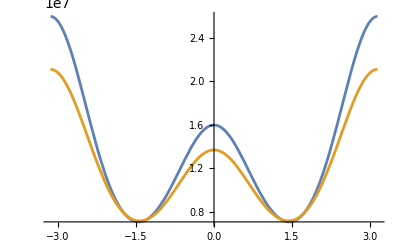

```mathematica
F2[ki_,kj_,xij_]:=5/7+2/7 xij^2 +xij/2(ki/kj+kj/ki);
G2[ki_,kj_,xij_]:=3/7+4/7 xij^2 +xij/2(ki/kj+kj/ki);
Z1[mu_,k_,b_,c1_,f_]:=b+mu^2 f - c1 k^2 mu^2;

mu2f[x_,mu1_,phi_]:=-Sqrt[1-mu1^2] Sqrt[1-x^2] Cos[phi]+mu1 x;
mu3f[k1_,k2_,k3_,x_,mu1_,phi_]:=-k1/k3 mu1-k2/k3 mu2f[x,mu1,phi];
k3f[k1_,k2_,k3_,x_]:=Sqrt[k1^2+k2^2+2 k1 k2 x];
xf[k1_,k2_,k3_]:=(k3^2-k1^2-k2^2)/(2 k1 k2);
x13[k1_,k2_,k3_,x_]:=-(k1+k2 x)/k3;
x23[k1_,k2_,k3_,x_]:=-(k2+k1 x)/k3;

muij[ki_,kj_,xij_,mui_,muj_]:=(ki mui +kj muj)/Sqrt[ki^2+kj^2+2 ki*kj xij];

Qij[ki_,kj_,xij_,mui_,muj_,f_,b1_,b2_,bs_,c1_]:=2(b1 F2[ki,kj,xij] + f (ki mui +kj muj)^2/(ki^2+kj^2+2 ki*kj xij)G2[ki,kj,xij] +(ki mui + kj muj)/2(mui/ki f(b1+f muj^2)+muj/kj f(b1+f mui^2))+bs(xij-1/3)+b2/2)Z1[mui,ki,b1,c1,f]Z1[muj,kj,b1,c1,f];

Qij$reduced[ki_,kj_,xij_,mui_,muj_,f_,b1_,b2_,bs_,c1_]:=2(b1 F2[ki,kj,xij] + f ((ki mui +kj muj)/Sqrt[ki^2+kj^2+2 ki*kj xij])^2G2[ki,kj,xij] +(ki mui + kj muj)/2(mui/ki f(b1+f muj^2)+muj/kj f(b1+f mui^2))+bs(xij-1/3)+b2/2)*(b1^2+b1 (f-c1 ki^2) mui^2+b1 (f-c1 kj^2) muj^2+f (f-c1 (ki^2+kj^2)) mui^2 muj^2);

Qijf[ki_,kj_,xij_,mui_,muj_,f_,b1_,b2_,bs_,c1_]:=2 (b1+f mui^2-c1 ki^2 mui^2) (b1+f muj^2-c1 kj^2 muj^2) (b2/2+1/2 (ki mui+kj muj) ((f muj (b1+f mui^2))/kj+(f mui (b1+f muj^2))/ki)+bs (-1/3+xij^2)+b1 (5/7+1/2 (ki/kj+kj/ki) xij+(2 xij^2)/7)+(f (ki mui+kj muj)^2 (3/7+1/2 (ki/kj+kj/ki) xij+(4 xij^2)/7))/(ki^2+kj^2+2 ki kj xij));


bispectrumM[k1_,k2_,x12_,mu1_,phi_,f_,b1_,b2_,bs_,c1_,qpar_,qperp_]:=Module[{k3,mu2,mu3,x13,x23,k1AP,k2AP,k3AP,mu1AP,mu2AP,mu3AP,pk1,pk2,pk3,Q12,Q23,Q13,B12,B23,B13,FAP,bispectrum},

mu2=-Sqrt[1-mu1^2] Sqrt[1-x12^2] Cos[phi]+mu1 x12;
k3=Sqrt[k1^2+k2^2+2 k1 k2 x12];
mu3=-k1/k3 mu1-k2/k3 mu2;

x13=-(k1+k2 x12)/k3;
x23=-(k2+k1 x12)/k3;

FAP=qpar/qperp;
k1AP=(k1/qperp)*(1+mu1^2*(1./FAP^2-1))^0.5;
mu1AP=(mu1/FAP)*(1+mu1^2*(1/FAP^2-1))^(-0.5);
k2AP=(k2/qperp)*(1+mu2^2*(1./FAP^2-1))^0.5;
mu2AP=(mu2/FAP)*(1+mu2^2*(1/FAP^2-1))^(-0.5);
k3AP=(k3/qperp)*(1+mu3^2*(1./FAP^2-1))^0.5;
mu3AP=(mu3/FAP)*(1+mu3^2*(1/FAP^2-1))^(-0.5);

Q12=Qijf[k1AP,k2AP,x12,mu1AP,mu2AP,f,b1,b2,bs,c1];
Q13=Qijf[k1AP,k3AP,x13,mu1AP,mu3AP,f,b1,b2,bs,c1];
Q23=Qijf[k2AP,k3AP,x23,mu2AP,mu3AP,f,b1,b2,bs,c1];

pk1=pkl[k1AP];
pk2=pkl[k2AP];
pk3=pkl[k3AP];

B12=Q12*pk1*pk2;
B13=Q13*pk1*pk3;
B23=Q23*pk2*pk3;
bispectrum=B12+B13+B23;
bispectrum
];
k1v=0.1;k2v=0.2;
fv=0.7797171445808948;
b1v=1;b2v=8/21*(b1v-1);bsv=-4/7*(b1v-1)

Omv=0.3105814212519492;hv=0.67;
qparv=1;qperpv=1;
Bshotv=0.0;Pshotv=0.0;c1v=0;
x12v=0.3;mu1v=0.2;mu2v=-0.1;phiv=0.24;
bisp[k1_,k2_,x_,mu_,phi_]:=bispectrumM[k1,k2,x,mu,phi,fv,b1v,b2v,bsv,c1v,qparv,qperpv];
bisp[k1v,k2v,x12v,mu1v,phiv]
Plot[{bisp[k1v,k2v,x12v,mu1v,phiv],bisp[k2v,k1v,x12v,mu1v,phiv]},{phiv,-Pi,Pi}]
```

```mathematica
B000$integrand[k1_,k2_,x_,mu_,phi_]:=bisp[k1,k2,x,mu,phi]*1/(8*Pi)*1;
B110$integrand[k1_,k2_,x_,mu_,phi_]:=bisp[k1,k2,x,mu,phi]*(-(3 √3 x)/(8 π))*(-1/(√3));
B220$integrand[k1_,k2_,x_,mu_,phi_]:=bisp[k1,k2,x,mu,phi]*((5 √5 (-1+3 x^2))/(16 π))*1/(√5);
B202$integrand[k1_,k2_,x_,mu_,phi_]:=bisp[k1,k2,x,mu,phi]*(5 √5 (-1+3 mu^2))/(16 π)*1/(√5);
B022$integrand[k1_,k2_,x_,mu_,phi_]:=bisp[k1,k2,x,mu,phi]*(5 √5 ((-1+3 mu^2) (-1+3 x^2)-12 mu √(1-mu^2) x √(1-x^2) Cos[phi]+3 (-1+mu^2) (-1+x^2) Cos[2 phi]))/(32 π)*1/(√5);
B112$integrand[k1_,k2_,x_,mu_,phi_]:=bisp[k1,k2,x,mu,phi]*(3 √(5/2) (√3 (-1+3 mu^2) x-6 mu √(1-mu^2) √(1-x^2) Cos[phi]))/(8 π)*√(2/15);

Bl1l2L$integrand[k1_,k2_,x_,mu_,phi_]:={B000$integrand[k1,k2,x,mu,phi],B110$integrand[k1,k2,x,mu,phi],B220$integrand[k1,k2,x,mu,phi],B202$integrand[k1,k2,x,mu,phi],B022$integrand[k1,k2,x,mu,phi],B112$integrand[k1,k2,x,mu,phi]};

nint=Length@Bl1l2L$integrand[0.2,0.2,0.2,0.2,0.2];
zeros=ConstantArray[0,nint] ;

Bl1l2L[k1_,k2_,tablesGL_]:=Module[{phiGL,muGL,xGL,intAll,intphi,intmu,result},
phiGL=tablesGL[[1]];
xGL=tablesGL[[2]];
muGL=tablesGL[[3]];
intAll=zeros;
Do[
intmu=zeros;
Do[
intphi=zeros;
Do[
intphi=intphi+Bl1l2L$integrand[k1,k2,xGL[[xii,1]],muGL[[muii,1]],phiGL[[phiii,1]]]*phiGL[[phiii,2]];
,{phiii,1,Length@phiGL}];
intphi=2*intphi;
intmu=intmu+intphi*muGL[[muii,2]];
,{muii,1,Length@muGL}];
intAll=intAll+intmu*xGL[[xii,2]];
,{xii,1,Length@xGL}];
result=intAll;
result
];
```

```mathematica
kT={0.01,0.01487179,0.01974359,0.02461538,0.02948718,0.03435897,0.03923077,0.04410256,0.04897436,0.05384615,0.05871795,0.06358974,0.06846154,0.07333333,0.07820513,0.08307692,0.08794872,0.09282051,0.09769231,0.1025641,0.1074359,0.11230769,0.11717949,0.12205128,0.12692308,0.13179487,0.13666667,0.14153846,0.14641026,0.15128205,0.15615385,0.16102564,0.16589744,0.17076923,0.17564103,0.18051282,0.18538462,0.19025641,0.19512821,0.2};
```

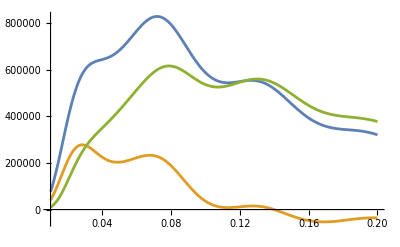

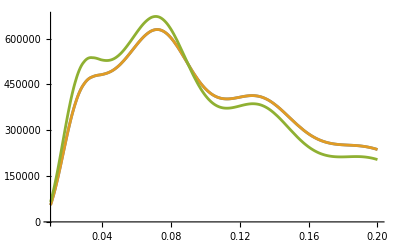

```mathematica
Nphi=8;Nx=10;Nmu=10;
phiGL=GaussianQuadratureWeights[Nphi,0,Pi];
xGL=GaussianQuadratureWeights[Nx,-1,1];
muGL=GaussianQuadratureWeights[Nmu,-1,1];
tablesGL={phiGL,xGL,muGL};
Bs=Table[Bl1l2L[kT[[i]],kT[[i]],tablesGL],{i,1,Length@kT}];

B000T=Table[{kT[[i]],Transpose[Bs][[1]][[i]]},{i,1,Length@kT}];
B000=Interpolation[B000T];
B110T=Table[{kT[[i]],Transpose[Bs][[2]][[i]]},{i,1,Length@kT}];
B110=Interpolation[B110T];
B220T=Table[{kT[[i]],Transpose[Bs][[3]][[i]]},{i,1,Length@kT}];
B220=Interpolation[B220T];
B202T=Table[{kT[[i]],Transpose[Bs][[4]][[i]]},{i,1,Length@kT}];
B202=Interpolation[B202T];
B022T=Table[{kT[[i]],Transpose[Bs][[5]][[i]]},{i,1,Length@kT}];
B022=Interpolation[B022T];
B112T=Table[{kT[[i]],Transpose[Bs][[6]][[i]]},{i,1,Length@kT}];
B112=Interpolation[B112T];

Plot[{(*k^2B000[k],*)k^2B000[k],k^2B110[k],k^2B220[k]},{k,0.01,0.20}]
Plot[{(*k^2B000[k],*)k^2B202[k],k^2B022[k],k^2B112[k]},{k,0.01,0.2}]
```

```mathematica
tabletoexp=Table[{kT[[i]],Transpose[Bs][[1]][[i]],Transpose[Bs][[2]][[i]],Transpose[Bs][[3]][[i]],Transpose[Bs][[4]][[i]],Transpose[Bs][[5]][[i]],Transpose[Bs][[6]][[i]]},{i,1,Length@kT}];
text={"# k, B000, B110, B220, B202, B022, B112"};
PrependTo[tabletoexp,text];
Export["Bl1l2L_mathematica.txt",tabletoexp,"Table"]
```

Bl1l2L_mathematica.txt